## Ayudantía 08-11.

### Ejercicio 1.

Generar un total de 1000 datos aleatorios que sigan la distribución de Gumbel, con función de densidad de probabilidad:

-Graphics-

Donde μ y β son variables, μ la moda y β actúa similar a la variancia.
Intente hacerlo tanto por funciones internas de Mathematica como manualmente como lo han visto en clases.

#### Manualmente

```mathematica
gumbel[x_,m_,b_]=E^(-(((x-m)/b)+
E^(-(x-m)/b)))/b
```

(ⅇ^(-ⅇ^((m-x)/b)-(-m+x)/b))/b

```mathematica
gumbelcdf[x_,m_,b_]=Integrate[gumbel[t,m,b],{t,0,x}]
```

-ⅇ^(-ⅇ^(m/b))+ⅇ^(-ⅇ^((m-x)/b))

```mathematica
Show[
Plot[gumbel[x,1,0.5],{x,-2,5},PlotStyle->Red,PlotRange->All],
Plot[gumbelcdf[x,1,0.5],{x,-2,5},PlotStyle->Blue]
]
```

-Graphics-

```mathematica
u0:=RandomReal[];
aux1=Table[FindRoot[{gumbelcdf[x,2,0.8]==u0},{x,2}],{c,1000}]//Quiet;
randnums=aux1[[All,1,2]];
```

#### A traves de funciones internas de Mathematica.

```mathematica
gumbeldist=ProbabilityDistribution[gumbel[x,2,0.8],{x,-1,7}]
```

ProbabilityDistribution[1.25 ⅇ^(-1.25 (-2+x)-ⅇ^(1.25 (2-x))),{x,-1,7}]

```mathematica
randnums2=RandomVariate[gumbeldist,1000];
```

#### Ambos casos comparados:

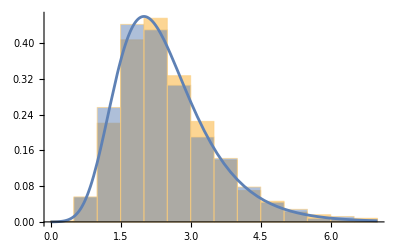

```mathematica
Show[Histogram[{randnums,randnums2},{0,7,0.5},"PDF"],Plot[gumbel[x,2,0.8],{x,0,7}]]
```

### Ejercicio 2:

Ahora, teniendo una serie de datos generados, intente ajustar una distribución a los mismos, primero utilizando FindDistribution, encuentre 5 modelos y compárelos con el histograma ajustado, en formato:

Histogram[randoms , Automatic , "PDF"]

Luego proponga usted un modelo a ajustar, siguiendo o no las sugerencias de FindDistribution y utilice OLS y MLE para encontrar las variables de los mismos, compare en un único gráfico.

```mathematica
finddists=FindDistribution[randnums,5]
```

{ExtremeValueDistribution[2.09404,0.871332],LogNormalDistribution[0.86417,0.437499],FrechetDistribution[21.1585,18.1517,-16.08],GammaDistribution[5.45637,0.477979],InverseGaussianDistribution[2.60803,12.2068]}

```mathematica
finddists[[1,2]]
```

0.871332

{Hue[Rational[1, 6], 0.5, 0.8],Hue[Rational[1, 3], 0.5, 0.8],Hue[Rational[1, 2], 0.5, 0.8],Hue[Rational[2, 3], 0.5, 0.8],Hue[Rational[5, 6], 0.5, 0.8],Hue[1, 0.5, 0.8]}

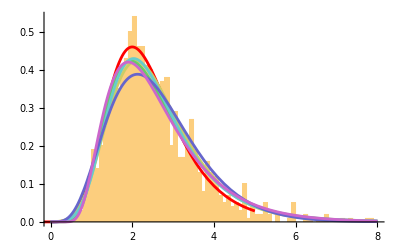

```mathematica
Table[Hue[k/6,0.5,0.8],{k,6}]
Show[
Histogram[randnums,{0,8,0.1},"PDF"],
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Table[
Plot[PDF[finddists[[k]],x],{x,0,8},PlotStyle->Hue[k/6,0.5,0.8]],{k,5}]
]
```

```mathematica
dist=SmoothKernelDistribution[randnums];
model=ExtremeValueDistribution[a,b];
```

```mathematica
mincuad=Sum[(PDF[dist,randnums[[k]]]-PDF[model,randnums[[k]]])^2,{k,Length@randnums}];
```

```mathematica
solOLS=FindMinimum[mincuad,{{a,0.5},{b,0.5}}]
```

{0.122654,{a→2.06331,b→0.824792}}

```mathematica
likehood=LogLikelihood[model,randnums];
solMLE=FindMaximum[likehood,{{a,0.5},{b,0.5}}]
```

{-1383.98,{a→2.05587,b→0.820058}}

```mathematica
solOLS[[2,1,2]]
```

2.06331

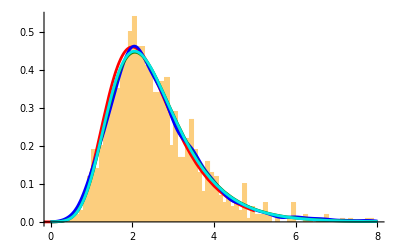

```mathematica
Show[
Histogram[randnums,{0,8,0.1},"PDF"],
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Plot[PDF[dist,x],{x,0,8},PlotStyle->Blue],
Plot[PDF[ExtremeValueDistribution[a,b],x]/.solOLS[[2]],{x,0,8},PlotStyle->Hue[0.3,1,0.5]],
Plot[PDF[ExtremeValueDistribution[a,b],x]/.solMLE[[2]],{x,0,8},PlotStyle->Hue[0.5,1,0.9]]
]
```

### Ejercicio 3

Vuelva a ajustar un modelo esta vez a un nuevo set de datos provenientes del ejercicio 1, hágalo extrayendo un total de 100 datos y un total de 100.000 datos, compare ambos casos con la distribución original (tener en cuenta que 100.000 tomará bastante tiempo en hacer el fit). Comente las diferencias en ambos casos.

```mathematica
data100=RandomVariate[gumbeldist,100];
data10000=RandomVariate[gumbeldist,100000];
```

```mathematica
finddists100=FindDistribution[data100,3]
finddists10000=FindDistribution[data10000,3]
```

{MixtureDistribution[{0.437738,0.562262},{NormalDistribution[1.99498,0.409622],NormalDistribution[3.07707,1.30227]}],GammaDistribution[5.15516,0.505007],ExtremeValueDistribution[2.08092,0.912783]}

{MixtureDistribution[{0.685205,0.314795},{NormalDistribution[1.91643,0.579969],LogNormalDistribution[1.26843,0.242458]}],MixtureDistribution[{0.70799,0.29201},{NormalDistribution[2.00626,0.659003],GammaDistribution[10.688,0.335312]}],MixtureDistribution[{0.00331127,0.996689},{LogisticDistribution[259042.,503310.],LogNormalDistribution[0.815544,0.432041]}]}

```mathematica
dist100=SmoothKernelDistribution[data100];
model100=GammaDistribution[a1,b1];
mincuad100=Sum[(PDF[dist100,data100[[k]]]-PDF[model100,data100[[k]]])^2,{k,Length@data100}];
solOLS100=FindMinimum[mincuad100,{{a1,0.5},{b1,0.5}}];
```

```mathematica
dist10000=SmoothKernelDistribution[data10000];
model10000=GammaDistribution[a2,b2];
mincuad10000=Sum[(PDF[dist10000,data10000[[2k]]]-PDF[model10000,data10000[[2k]]])^2,{k,Length@data10000/2}];
```

Para poder ejemplificar, es necesario por mi lado tener menos números a los que hacer el fit, por lo que en la última línea estaré tomando 1 dato de cada 2, los 2 al lado de los k y el dividido 2 en el final no deberían estar ahí en su solución.

```mathematica
solOLS10000=FindMinimum[mincuad10000,{{a2,0.5},{b2,0.5}}];
```

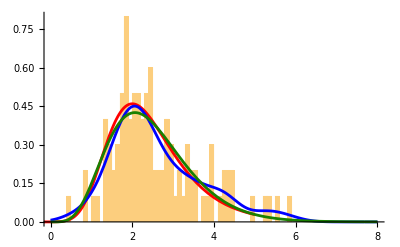

```mathematica
Show[
Histogram[data100,{0,8,0.1},"PDF"],
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Plot[PDF[dist100,x],{x,0,8},PlotStyle->Blue],
Plot[PDF[GammaDistribution[a1,b1],x]/.solOLS100[[2]],{x,0,8},PlotStyle->Hue[0.3,1,0.5]]
]
```

```mathematica
Show[
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Plot[PDF[GammaDistribution[a1,b1],x]/.solOLS100[[2]],{x,0,8},PlotStyle->Hue[0.3,1,0.5]]
]
```

-Graphics-

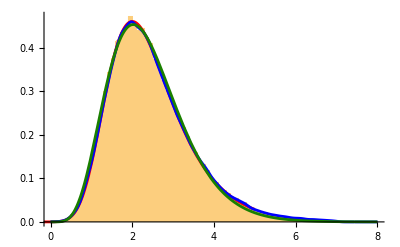

```mathematica
Show[
Histogram[data10000,{0,8,0.1},"PDF"],
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Plot[PDF[dist10000,x],{x,0,8},PlotStyle->Blue],
Plot[PDF[GammaDistribution[a2,b2],x]/.solOLS10000[[2]],{x,0,8},PlotStyle->Hue[0.3,1,0.5]]
]
```

```mathematica
Show[
Plot[gumbel[x,2,0.8],{x,-2,5},PlotStyle->Red],
Plot[PDF[GammaDistribution[a2,b2],x]/.solOLS10000[[2]],{x,0,8},PlotStyle->Hue[0.3,1,0.5]]
]
```

-Graphics-